Order eigenvalues and eigenvectors of a matrix by increasing eigenvalue.

```mathematica
M=Table[N@Abs[i-j],{i,10},{j,10}];
{val,vec}=Eigensystem[M]
```

{{34.3429,-20.4317,-6.51138,-2.42592,-1.50531,-1.,-0.772216,-0.629808,-0.553974,-0.512543},{{-0.407454,-0.340637,-0.293658,-0.26378,-0.249264,-0.249264,-0.26378,-0.293658,-0.340637,-0.407454},{0.441708,0.39847,0.316228,0.203031,0.0699596,-0.0699596,-0.203031,-0.316228,-0.39847,-0.441708},{0.388678,0.182921,-0.0790215,-0.316692,-0.457089,-0.457089,-0.316692,-0.0790215,0.182921,0.388678},{0.39847,0.0699596,-0.316228,-0.441708,-0.203031,0.203031,0.441708,0.316228,-0.0699596,-0.39847},{0.33058,-0.182102,-0.452837,-0.121918,0.370985,0.370985,-0.121918,-0.452837,-0.182102,0.33058},{0.316228,-0.316228,-0.316228,0.316228,0.316228,-0.316228,-0.316228,0.316228,0.316228,-0.316228},{0.240175,-0.435238,0.0165933,0.425449,-0.267586,-0.267586,0.425449,0.0165933,-0.435238,0.240175},{0.203031,-0.441708,0.316228,0.0699596,-0.39847,0.39847,-0.0699596,-0.316228,0.441708,-0.203031},{-0.126266,0.35765,-0.449648,0.366409,-0.140372,-0.140372,0.366409,-0.449648,0.35765,-0.126266},{-0.0699596,0.203031,-0.316228,0.39847,-0.441708,0.441708,-0.39847,0.316228,-0.203031,0.0699596}}}

{{-20.4317,-6.51138,-2.42592,-1.50531,-1.,-0.772216,-0.629808,-0.553974,-0.512543,34.3429},{{0.441708,0.39847,0.316228,0.203031,0.0699596,-0.0699596,-0.203031,-0.316228,-0.39847,-0.441708},{0.388678,0.182921,-0.0790215,-0.316692,-0.457089,-0.457089,-0.316692,-0.0790215,0.182921,0.388678},{0.39847,0.0699596,-0.316228,-0.441708,-0.203031,0.203031,0.441708,0.316228,-0.0699596,-0.39847},{0.33058,-0.182102,-0.452837,-0.121918,0.370985,0.370985,-0.121918,-0.452837,-0.182102,0.33058},{0.316228,-0.316228,-0.316228,0.316228,0.316228,-0.316228,-0.316228,0.316228,0.316228,-0.316228},{0.240175,-0.435238,0.0165933,0.425449,-0.267586,-0.267586,0.425449,0.0165933,-0.435238,0.240175},{0.203031,-0.441708,0.316228,0.0699596,-0.39847,0.39847,-0.0699596,-0.316228,0.441708,-0.203031},{-0.126266,0.35765,-0.449648,0.366409,-0.140372,-0.140372,0.366409,-0.449648,0.35765,-0.126266},{-0.0699596,0.203031,-0.316228,0.39847,-0.441708,0.441708,-0.39847,0.316228,-0.203031,0.0699596},{-0.407454,-0.340637,-0.293658,-0.26378,-0.249264,-0.249264,-0.26378,-0.293658,-0.340637,-0.407454}}}

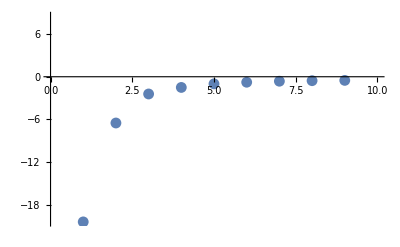

```mathematica
{val[[#]],vec[[#]]}&@Ordering[val]
ListPlot[%[[1]]]
```